# Dynamics of rotating and precessing neutron stars

## Equation of motion

The configuration of the rigid body. (X-Y-Z is the inertia frame, x1-x2-x3 is the body frame)

The angular velocity can be described by three Euler angles

Ω_x==ϕ̇ sinθsinψ+θ̇ cosψ
Ω_y==ϕ̇ sinθcosψ-θ̇ sinψ
Ω_z==ϕ̇ cosθ+ψ̇

The dynamical equation of force free rigid body is

|  I_1(d Ω_1)/dt==(I_2-I_3)Ω_2 Ω_3 
                                   |  I_2(d Ω_2)/dt==(I_3-I_1)Ω_3 Ω_1 
   |  I_3(d Ω_3)/dt==(I_1-I_2)Ω_1 Ω_2

## Axisymmetric deformation and free precession

We consider an axisymmetric neutron star with I_1  = I_2 = I, not equal to I_3. The dynamical equation of Ω_3 is

Ω_3 = Ω Cos[θ] = Const.

In the inertia frame, angular momentum J, axisymmetric axis x_3 and angular velocity Ω are coplanar.   Ω  and x_3 orbit around J at ϕ̇, and the rigid body spin around the axisymmetric axis at the angular velocity (I-I_3)/IΩ_3, which is called free precession angular velocity.

The rotation around x_3 does not radiate gravitational waves, because the rigid body is axisymmetric. For pulsars, this frequency could be in LISA band. What if neutron star is deformed into a triaxial ellipsoid and does free precession? Can the gravitational-wave frequency falls into LISA band? For the first step, we need to  calculate the dynamics of this object.

## Free precession of triaxial ellipsoid

### Qualitative analysis

We have two first integrals, energy and angular momentum.

J_1^2/(2 I_1 E) + J_1^2/(2 I_2 E) + J_1^2/(2 I_3 E) = 1
J_1^2 + J_2^2 + J_3^2 = J^2

In body frame, we can draw an energy ellipsoid and an angular momentum sphere.

Define I_1< I_2< I_3, and the angular momentum vector can only move on the intersecting line, which tells us

2E I_1 < J^2 < 2E I_3

1. When 2E I_1 < J^2 << 2E I_2 , the spinning ellipsoid is stable around x_1

2. When  2E I_1 <<J^2 = 2E I_2 , the spinning ellipsoid is not stable, the angular momentum vector moves in a great circle. This effect can make the force free rigid body twist around, which is called tennis-racket effect, or Janibekov effect (a Soviet astronaut, who found this bizarre effect in spacecraft)

### Analytical solution in body frame

#### 1. J^2 - 2E I_2 > 0

We have three Euler equations, we can substitute two equations with two first integrals. It shows that

Ω_1^2 |  ==[(2E I_3-J^2)-I_2(I_3-I_2)Ω_2^2]/(I_1(I_3-I_1)) 
Ω_3^2 | ==[(J^2-2E I_1)-I_2(I_2-I_1)Ω_2^2]/(I_3(I_3-I_1))

and Ω_2 satisfies

-Graphics-

We define

|                   τ==t √(((I_3-I_2)(J^2-2E I_1))/(I_1 I_2 I_3)) 
                                    |  s==Ω_2 √((I_2(I_3-I_2))/(2E I_3-J^2))
   |            k^2==((I_2-I_1)(2E I_3-J^2))/((I_3-I_2)(J^2-2E I_1))

Integrate the differential equation of Ω_2, we could find that

τ =  ∫_0^s ds/(√((1-s^2)(1-k^2 s^2)))ⅆs

This is a Jacobian elliptical function.

s is Jacobian amplitude and k is called elliptic modulus.  The inverse of the elliptical gives us the time evolution of s.

s = sn(τ),   cn(τ) = √(1-sn^2 τ) ,  dn(τ) = √(1 - k^2 sin^2 τ)

According to the definition of Jacobian  function, these three functions are periodic function of τ, the period is

T = 4 K

where K is called elliptic integrals of the first kind.

K = ∫_0^1 ds/(√((1-s^2)(1-k^2 s^2)))ⅆs

0.890615

6.93567

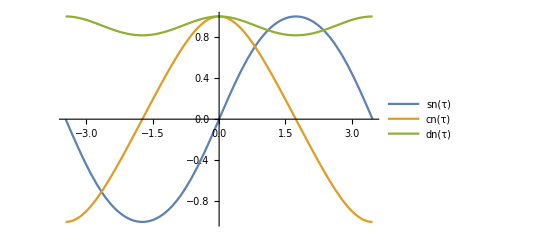

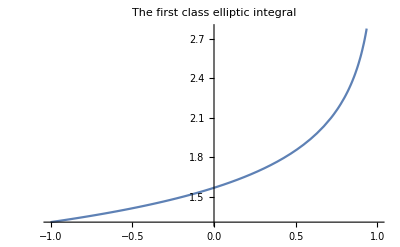

```mathematica
T=4*EllipticK[1./3]
Plot[{JacobiSN[x,1./3],JacobiCN[x,1./3],JacobiDN[x,1./3]},{x,-T/2,T/2}, PlotLegends->{"sn(τ)", "cn(τ)", "dn(τ)"}]
Plot[EllipticK[x],{x,-1,1},PlotLabel->"The first class elliptic integral"]
```

The evolution of the angular velocities are

Ω_1(τ) = √((2E I_3-J^2)/(I_1(I_3-I_1))) cn(τ)
Ω_2(τ) = √((2E I_3-J^2)/(I_2(I_3-I_2))) sn(τ)
Ω_3(τ) = √((J^2-2E I_1)/(I_3(I_3-I_1))) dn(τ)

#### Why plants and stars do not show tennis-rocket effect

Planets, like Mars and the Earth do not show tennis rocket effect. They don’t flip around when they rotate. The reason is that kinetic energy is not conserved, they can be dissipated into heat or something. Roughly speaking, the angular momentum is conserved. E = J^2/(2I), if the body is spinning around the smallest moment of inertia axis, the energy is largest. After dissipation, the kinetic energy goes down. It must rotate around the largest moment of inertia axis, which has the lowest energy state.

10119.1

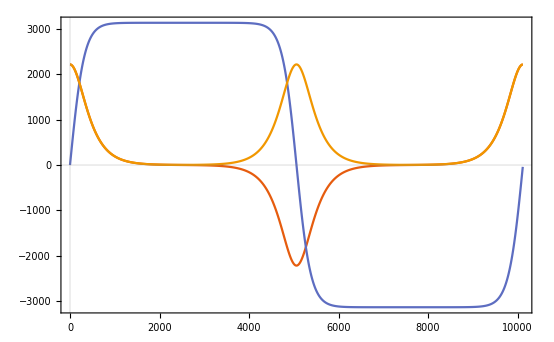

```mathematica
I1=1-10^-6;
I2=1.0;
I3=1+10^-6;
a=π*1000*N[Sin[π/4]];w20=0;b=π*1000*N[Cos[π/4]];
J= (I1^2*a^2+I2^2*w20^2+I3^2*b^2)^0.5;
E0=1/2 I1*a^2+1/2 I2*w20^2+1/2 I3*b^2;
k2=((I2-I1)(2E0*I3-J^2))/((I3-I2)(J^2-2E0*I1));
taut=√(((I3-I2)(J^2-2E0*I1))/(I1*I2*I3));
K=EllipticK[k2];
T=4*K*((I1*I2*I3)/((I3-I2)*(J^2-2*E0*I1)))^0.5
w1=Table[a*JacobiCN[t*taut,k2],{t,0,T,5}];
w2=Table[a*√((I1(I3-I1))/(I2(I3-I2)))*JacobiSN[t*taut,k2],{t,0,T,5}];
w3=Table[b*JacobiDN[t*taut,k2],{t,0,T,5}];

time= Table[t1,{t1,0,T,5}];
data1=Transpose@{time,w1};
data2=Transpose@{time,w2};
data3=Transpose@{time,w3};
ListPlot[{data1,data2, data3},Joined->True,PlotTheme->"Scientific"]
```

#### 2. J^2 - 2E I_2 = 0

In this case, k^2 = 1. The elliptic functions turn into hyperbolic functions.

sn(τ, 1) = tanhτ ,    cn(τ, 1) = sechτ,    dn(τ, 1) = sechτ

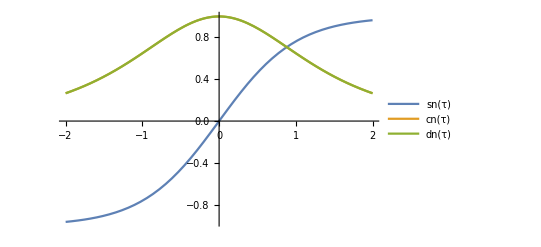

```mathematica
Plot[{JacobiSN[x,1],JacobiCN[x,1],JacobiDN[x,1]},{x,-2,2}, PlotLegends->{"sn(τ)", "cn(τ)", "dn(τ)"}]
```

In this case

ds/dτ = 1 - s^2,     τ = t √(((I_2-I_1)(I_3-I_2))/(I_1 I_3)) Ω_0,     s = Ω_2/Ω_0

The evolution of three angular velocities are

Ω_1 = Ω_0√((I_2(I_3-I_2))/(I_1(I_3-I_1)))1/coshτ
Ω_2 = Ω_0 tanhτ
Ω_3==Ω_0 √((I_2(I_2-I_1))/(I_3(I_3-I_1)))1/coshτ

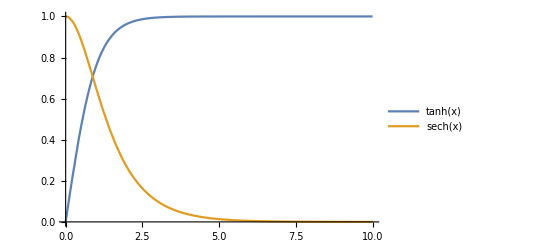

```mathematica
Plot[{Tanh[x],Sech[x]}, {x,0,10},PlotLegends->"Expressions"]
```

#### 3. J^2 - 2E I_2 < 0

This condition is similar to the first condition, just exchange index 1 ans 3

### Analytical solutions in inertia frame

Because J is the Z axis, and we can decompose the angular momentum with three Euler angles

|                                                Jsinθsinψ==J_1==I_1 Ω_1
Jsinθcosψ==J_2==I_2 Ω_2
Jcosθ==J_3==I_3 Ω_3 
   |                                             cosθ==(I_3 Ω_3)/J,  tanψ==(I_1 Ω_1)/(I_2 Ω_2)

And from the solutions above, we can obtain

|                                               cosθ==√((I_3(J^2-2E I_1))/(J^2(I_3-I_1)))dnτ 
   |                                              tanψ==√((I_1(I_3-I_2))/(I_2(I_3-I_1)))cnτ/snτ

Both are periodic functions of τ, and the period is also T=4K

In order to calculate ϕ, we need another two equations

Ω_1==ϕ̇ sinθsinψ+θ̇ cosψ
          Ω_2==ϕ̇ sinθcosψ-θ̇ sinψ

Eliminate θ,

dϕ/dt==J(I_1 Ω_1^2+I_2 Ω_2^2)/(I_1^2 Ω_1^2+I_2^2 Ω_2^2)

This equation is a complex combination of elliptic function. The result can be expressed as ϕ = ϕ_1 + ϕ_2

exp[2iϕ_1(t)]==(ϑ_4((2πt)/T-iπα,q))/(ϑ_4((2πt)/T+iπα,q))

where ϑ_4 is Jacobian Θ function , and α satisfies

sn(i·2αK)==i √((I_3(J^2-2E I_1))/(I_1(2E I_3-J^2)))

Where K is the elliptic function of the first kind. For ϕ_2

ϕ_2==(2π)/T' = J/I_1-(2i)/T(ϑ'_4(iπα))/(ϑ_4(iπα))

```mathematica
I1=1.9;I2=2.0;I3=2.1;
w1=3;w2=4;w3=5;
J= (I1^2*w1^2+I2^2*w2^2+I3^2*w3^2)^0.5
E0=1/2 I1*w1^2+1/2 I2*w2^2+1/2 I3*w3^2
```

14.3785

50.8

First, we need α, calculate K and the inverse of Jacobian function
                                                sn(i·2αK)==i √((I_3(J^2-2E I_1))/(I_1(2E I_3-J^2)))

```mathematica
k2=((I2-I1)(2E0*I3-J^2))/((I3-I2)(J^2-2E0*I1))
K=EllipticK[k2]
x1=I* ((I3(J^2-2E0*I1))/(I1(2E0*I3-J^2)))^0.5
α= Re[InverseJacobiSN[x1,k2]/I/K/2]
```

0.483212

1.84011

0.+1.51239 ⅈ

0.290716

Second, we need to calculate the  elliptic Θ function

exp[2iφ_1(t)]==(ϑ_4((2πt)/T-iπα,q))/(ϑ_4((2πt)/T+iπα,q))

In Θ function, we need to know a parameter q, 0<q<1.

q = e^(-π K'/K), and K' = K(1-k^2)

0.0411645

4.69161

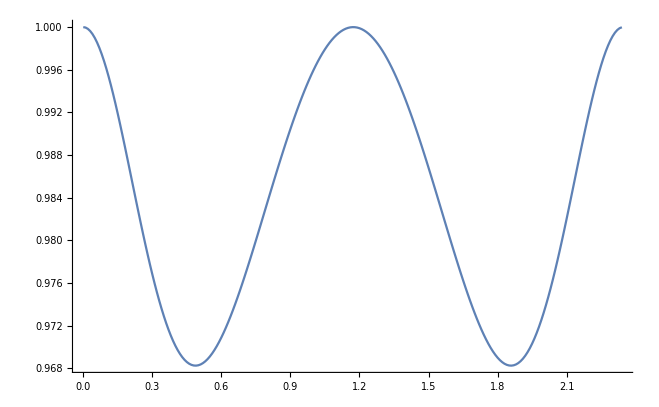

2.34581

```mathematica
q= Exp[-π* EllipticK[1-k2]/EllipticK[k2]]
T=4*K*((I1*I2*I3)/((I3-I2)*(J^2-2*E*I1)))^0.5
a=Table[Re[EllipticTheta[4,2*π/T*t-π*α*I,q]/EllipticTheta[4,2.*π/T*t+π*α*I,q]],{t,0,T/2,0.01}];
b=Table[Im[EllipticTheta[4,2.*π/T*t-π*α*I,q]/EllipticTheta[4,2.*π/T*t+π*α*I,q]],{t,0,T/2,0.01}];
angle11=ArcTan[a,b]/2;
time= Table[t,{t,0,T/2,0.01}];
data=Transpose@{time,Cos[angle11]};
ListPlot[data,Joined->True]
period1=T/2
```

The other part, ϕ_2 is also a periodic function

ϕ_2==(2π)/T' t  = (J/I_1-(2i)/T(ϑ'_4(iπα))/(ϑ_4(iπα))) t

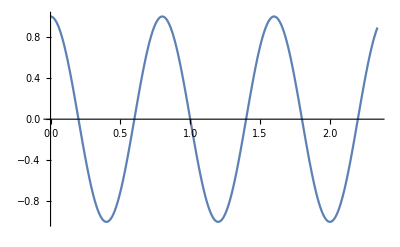

```mathematica
angle12=Re[Table[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])*t,{t,0,T/2,0.01}]];
data1=Transpose@{time,Cos[angle12]};
ListPlot[data1,Joined->True]
```

## Numerical method to calculate the equation of motion and Euler angles

### 1. Solve the evolution of angular velocities in body frame

The dynamical equation of force free rigid body is

I_1(d Ω_1)/dt==(I_2-I_3)Ω_2 Ω_3 
 I_2(d Ω_2)/dt==(I_3-I_1)Ω_3 Ω_1 
 I_3(d Ω_3)/dt==(I_1-I_2)Ω_1 Ω_2

Giving the initial value [Ω_1, Ω_2, Ω_3] and three moment of inertia [I_1, I_2, I_3], we can obtain the time evolution of three angular velocities.

```mathematica
{I1,I2,I3}={1-10^-6,1,1+10^-6};
sbody=NDSolve[{
I1 *w1 '[t]-(I2-I3)w2[t]*w3[t]==0,
I2 *w2 '[t]-(I3-I1)w3[t]*w1[t]==0,
I3 *w3 '[t]-(I1-I2)w1[t]*w2[t]==0,
w1[0]==2000*π*√2/2,
w2[0]==0,
w3[0]==2000*π*√2/2},
{w1,w2,w3},{t,0,10000}]
```

{{w1→InterpolatingFunction[…],w2→InterpolatingFunction[…],w3→InterpolatingFunction[…]}}

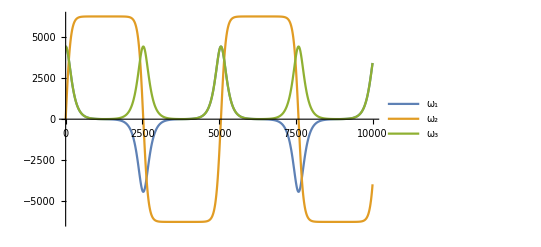

```mathematica
Plot[{w1[t]/.sbody[[1]],w2[t]/.sbody[[1]],w3[t]/.sbody[[1]]},{t,0,10000}
,PlotLegends->{Subscript[ω, 1], Subscript[ω, 2], Subscript[ω, 3]}]
```

{{w1→InterpolatingFunction[…],w2→InterpolatingFunction[…],w3→InterpolatingFunction[…]}}

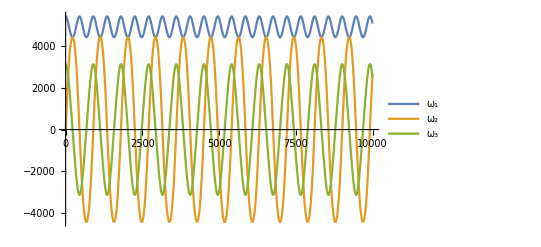

```mathematica
{I1,I2,I3}={1-10^-6,1,1+10^-6};
sbody=NDSolve[{
I1 *w1 '[t]-(I2-I3)w2[t]*w3[t]==0,
I2 *w2 '[t]-(I3-I1)w3[t]*w1[t]==0,
I3 *w3 '[t]-(I1-I2)w1[t]*w2[t]==0,
w1[0]==2000*π*Cos[π/6],
w2[0]==0,
w3[0]==2000*π*Sin[π/6]},
{w1,w2,w3},{t,0,10000}]
Plot[{w1[t]/.sbody[[1]],w2[t]/.sbody[[1]],w3[t]/.sbody[[1]]},{t,0,10000}
,PlotLegends->{Subscript[ω, 1], Subscript[ω, 2], Subscript[ω, 3]}]
```

{{w1→InterpolatingFunction[…],w2→InterpolatingFunction[…],w3→InterpolatingFunction[…]}}

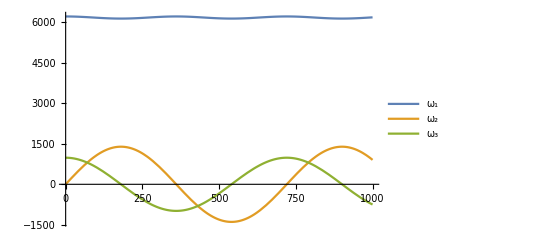

```mathematica
{I1,I2,I3}={1-10^-6,1,1+10^-6};
sbody=NDSolve[{
I1 *w1 '[t]-(I2-I3)w2[t]*w3[t]==0,
I2 *w2 '[t]-(I3-I1)w3[t]*w1[t]==0,
I3 *w3 '[t]-(I1-I2)w1[t]*w2[t]==0,
w1[0]==2000*π*Cos[π/20],
w2[0]==0,
w3[0]==2000*π*Sin[π/20]},
{w1,w2,w3},{t,0,10000}]
Plot[{w1[t]/.sbody[[1]],w2[t]/.sbody[[1]],w3[t]/.sbody[[1]]},{t,0,1000}
,PlotLegends->{Subscript[ω, 1], Subscript[ω, 2], Subscript[ω, 3]}]
```

Comparing with python code, I found the Mathematica NDSolve is very accurate, even for NS(the difference between I1, I2 and I3 are very small, about 10^-6)

We can test it with a axisymmetric top I_1 = I_2

```mathematica
{I1,I2,I3}={2,2,4};
sbody=NDSolve[{
I1 *w1 '[t]-(I2-I3)w2[t]*w3[t]==0,
I2 *w2 '[t]-(I3-I1)w3[t]*w1[t]==0,
I3 *w3 '[t]-(I1-I2)w1[t]*w2[t]==0,
w1[0]==4,
w2[0]==5,
w3[0]==3},
{w1,w2,w3},{t,0,5}]
```

{{w1→InterpolatingFunction[…],w2→InterpolatingFunction[…],w3→InterpolatingFunction[…]}}

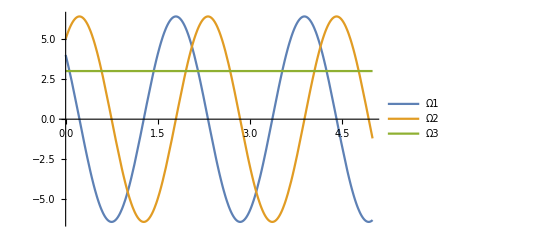

```mathematica
Plot[{w1[t]/.sbody[[1]],w2[t]/.sbody[[1]],w3[t]/.sbody[[1]]},{t,0,5}
,PlotLegends->{Ω1, Ω2, Ω3}]
```

### 2. Solve the Orientation in inertia frame

In principle, we have three kinetic equation. Integrating these equations we can get the Euler angles.

Ω_x==ϕ̇ sinθsinψ+θ̇ cosψ
Ω_y==ϕ̇ sinθcosψ-θ̇ sinψ
Ω_z==ϕ̇ cosθ+ψ̇

But there are two problems would occur.

1. The integration of Euler angles requires many evaluations of trigonometric functions, which are generally slower than multiplications.

2. There is a problem known as gimbal lock effect, where two of the rotational axes of an object merger together. After this happens, it is impossible to rotate about one of the three dimensions.

Mathematically, if the dimensions degenerate from three dimensions into two dimensions. The Euler angle representations only rely on the combinations of two angles, not two independent angles.

-Graphics-

In order to solve these two problem, we use quaternions to do rotation.

### Quaternions

We will define quaternions using a scalar and a three dimensional vector. We can write the quaternion as

q = [s, v] = [s, x i + y j + z k ], s ∈ R, v ∈ R^3

1. Additions and multiplications of quaternions

q1 =[ a1,b1],  q2= [a2, b2]
q1 + q2 = [a1 + a2, b1 + b2]
q1q2= [a1*a2-b1*b2, a1*b2 + a2*b1 + b1 × b2]

```mathematica
<<Quaternions`
```

```mathematica
a=Quaternion[1,2,3,4];
b=Quaternion[4,3,2,1];
a+b
a**b
```

Quaternion[5,5,5,5]

Quaternion[-12,6,24,12]

```mathematica
c=Sign[a]
Abs[c]
```

Quaternion[1/(√30),√(2/15),√(3/10),2 √(2/15)]

1

### Use Quaternions to do rotations

Theorem 1 : Let p, n_1 and n_2 be unit vectors. Let S_i be the reflection about a
plane passing through the origin, and normal to n_i. If n_2.02× n_1 is in the direction
p, then S_2 S_1 is a rotation about the line in the direction p. If the angle between
the vectors n_1 and n_2 is θ/2, then the rotation is by an angle of θ.12. In this case
we have n_1· n_2= cos(θ/2), and n2 × n1 = sin(θ/2)p.

Suppose we want to rotate by θ about a line passing through the origin, and
pointing in the direction p. The theorem 1 shows that we can accomplish this by performing the reflections S_2S_1 . In terms of quaternions this transformation maps the vector v to the vector

v' = n_2 n_1 v n_1 n_2 = q v q^-1

where

q =  n_2 n_1 = [cos θ/2, sin θ/2 p]

This quaternion represents a rotation of angle θ  about a given vector p

### Representation of unit quaternion as 3×3 orthogonal matrix

q =[q_0, q_1, q_2, q_3]

r' = q r q^-1 = A r

After some calculations, we could get

A = 2 (q_0^2 + q_1^2- q_2^2- q_3^2 | q_1 q_2-q_0 q_3 | q_1 q_3+q_0 q_2
q_1 q_2+q_0 q_3 | q_0^2 - q_1^2+ q_2^2- q_3^2 | q_2 q_3-q_0 q_1
q_1 q_3-q_0 q_2 | q_2 q_3+q_0 q_1 | q_0^2 - q_1^2- q_2^2+ q_3^2)

### Use quaternions to do numerical integrations of Euler equations

First, we need to know the time evolution of quaternions. Here we just give the result.
Ref: 
1. The Quaternions with an application to Rigid Body Dynamics, Evangelos A. Coutsias, University of New Mexico.
2. Simulations of Rigid Body Dynamics in Matlab, Varun Ganapathi, Stanford University

Together with the three dynamical equations

I_1(d Ω_1)/dt==(I_2-I_3)Ω_2 Ω_3 
 I_2(d Ω_2)/dt==(I_3-I_1)Ω_3 Ω_1 
 I_3(d Ω_3)/dt==(I_1-I_2)Ω_1 Ω_2

1. Give initial condition: three angular velocities in body frame, the orientation of the body(three Euler angles, can be converted to four items of quaternion.);
2. Integrate these seven equations to get the evolution of Ω and q;
3. Get the rotation matrix, and we know the rotation matrix can also be represented as

```mathematica
EulerMatrix[{ϕ, θ, ψ},{3,1,3}]//MatrixForm
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | -Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ϕ]
Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | -Cos[ϕ] Sin[θ]
Sin[θ] Sin[ψ] | Cos[ψ] Sin[θ] | Cos[θ])

Match with 
                     A = 2 ((q_0^2 + q_1^2- q_2^2- q_3^2)/2 | q_1 q_2-q_0 q_3 | q_1 q_3+q_0 q_2
q_1 q_2+q_0 q_3 | (q_0^2 - q_1^2+ q_2^2- q_3^2)/2 | q_2 q_3-q_0 q_1
q_1 q_3-q_0 q_2 | q_2 q_3+q_0 q_1 | (q_0^2 - q_1^2- q_2^2+ q_3^2)/2),

do some calculations, we obtain quaternions can be represented by Euler angles

q_0==cos 1/2 θ cos(1/2(ϕ+ψ))
q_1==sin 1/2 θ cos(1/2(ϕ-ψ))
q_2==sin 1/2 θ sin(1/2(ϕ-ψ))
q_3==cos 1/2 θ sin(1/2(ϕ+ψ))

The three Euler angles can be represented by matrix elements

|                                                      ϕ==tan^-1(-A_13/A_23) 
   |                                                            θ==tan^-1((√(1-A_33^2))/A_33) 
 |                                                   ψ==tan^-1(A_31/A_32)